```mathematica
Needs["NDSolve`FEM`"];
ClearAll[ sol,kappa,T0,Ptot,x,y,z,x0,y0,z0,sx,sy,sz,Lzrad,Rrad, Lstick, Hstick, Wstick, NormIntegral,powerDensity3DFunc, powerDensity3D];
```

```mathematica
$Assumptions=Lstick∈Reals&&Lstick>0&&Wstick∈Reals&&Wstick>0 &&Hstick∈Reals&&Hstick>0 &&x0∈Reals&&y0∈Reals&& z0∈Reals&&z0≥0&&z0≤Lstick;
```

```mathematica
powerDensity3DFunc[r_,θ_,z_]:=Piecewise[{{1.0, z≥z0&&z≤Lstick}},0];
```

```mathematica
NormIntegral=Integrate[powerDensity3DFunc[x,y,z],{x,x0-Wstick/2,x0+Wstick/2},{y,y0-Hstick/2,y0+Hstick/2},{z,0,Lstick}]
```

Piecewise[{{Hstick Lstick Wstick, Hstick>0.&&Lstick>0.&&Wstick>0.&&z0==0.}, {Hstick Wstick (Lstick-1. z0), Hstick>0.&&Lstick>0.&&Wstick>0.&&z0>0.&&Lstick-1. z0>0.}, {0., True}}]

```mathematica
kappa=0.00385;T0=50.0; Ptot=0.015; 
x0=0;y0=0; z0=Lstick-1;
(*Lzrad=0.15;*) Lzrad=1; Rrad=1.0;
Lstick=100;Hstick=2;Wstick=1;
```

```mathematica
NormIntegral
```

2.

```mathematica
powerDensity3D[x_,y_,z_]:= Ptot/NormIntegral*powerDensity3DFunc[x,y,z]
```

```mathematica
NIntegrate[powerDensity3D[x,y,z],{x,x0-Wstick/2,x0+Wstick/2},{y,y0-Hstick/2,y0+Hstick/2},{z,0,Lstick}]
```

0.015

```mathematica
Ptot/NormIntegral
```

0.0075

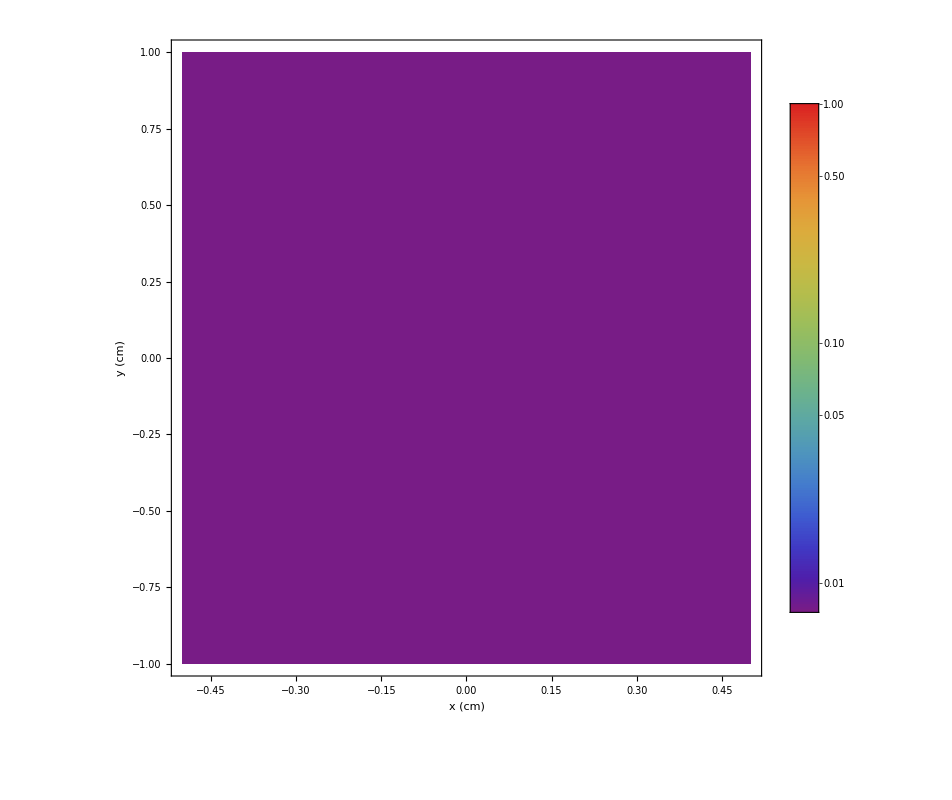

```mathematica
DensityPlot[powerDensity3D[x,y,z0],{x,x0-Wstick/2,x0+Wstick/2},{y,y0-Hstick/2,y0+Hstick/2},ColorFunction->{"Rainbow"},PlotRange->Full,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"x (cm)", "y (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

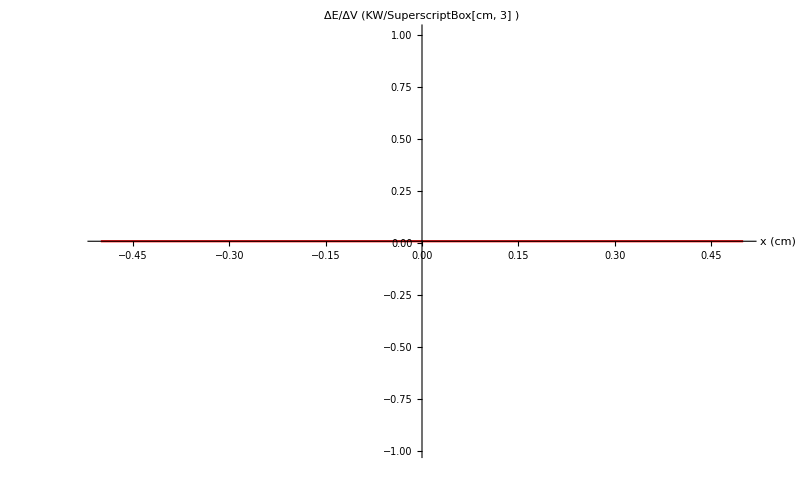

```mathematica
Plot[powerDensity3D[x,0,z0],{x,x0-Wstick/2,x0+Wstick/2}, AxesLabel->{"x (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.002]}]
```

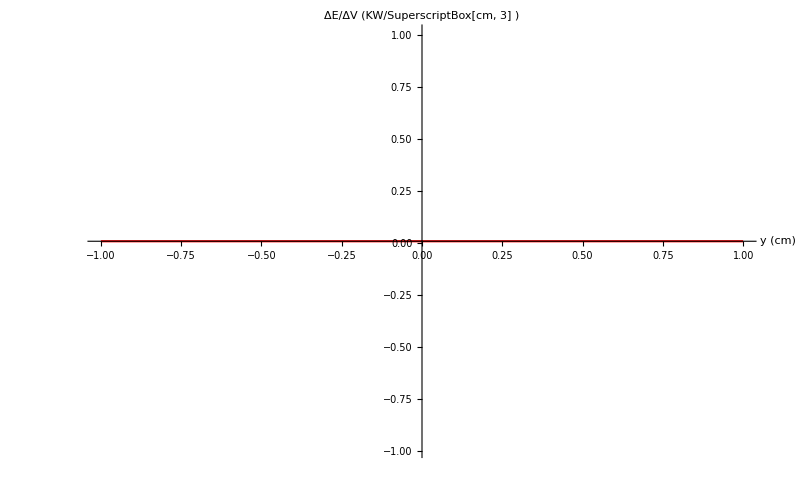

```mathematica
Plot[powerDensity3D[0,y,z0],{y,y0-Hstick/2,y0+Hstick/2}, AxesLabel->{"y (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.002]}]
```

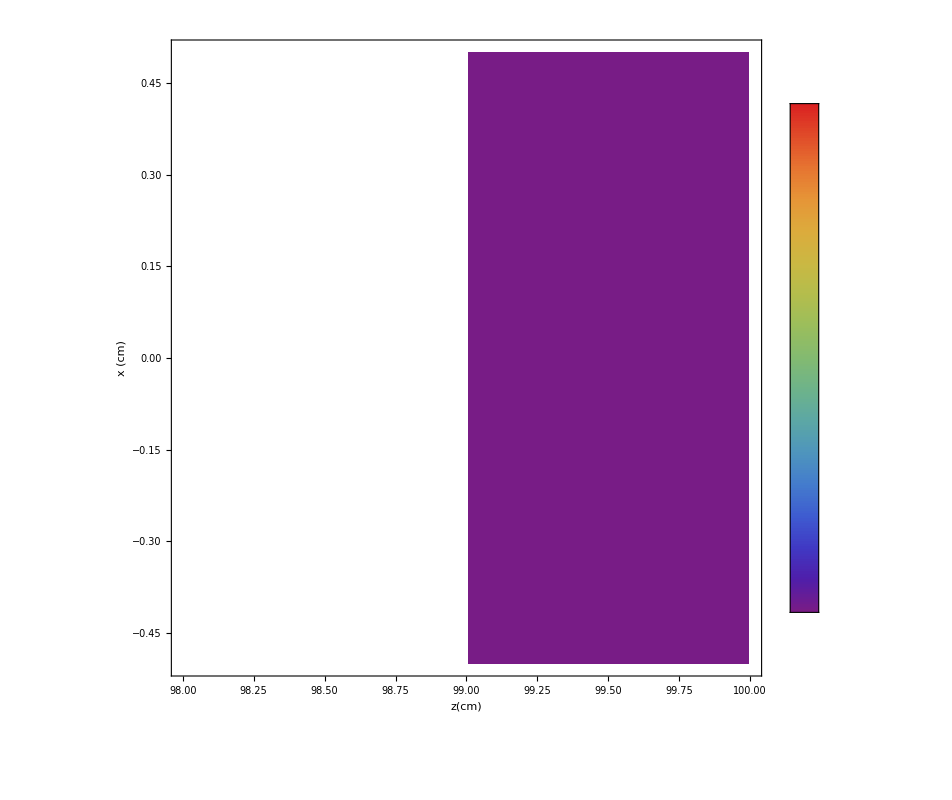

```mathematica
DensityPlot[powerDensity3D[x,0,z],{z,98,Lstick},{x,x0-Wstick/2,x0+Wstick/2},ColorFunction->"Rainbow",PlotRange->Full,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"z(cm)", "x (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

```mathematica
eqn=-Laplacian[u[x,y,z],{x,y,z}]==1/kappa*powerDensity3D[x,y,z]+ NeumannValue[0.0,x==Wstick/2||x==-Wstick/2||y==Hstick/2||y==-Hstick/2||z==0||z==Lstick];
```

```mathematica
sol=NDSolveValue[{eqn,{u[x,y,0]==T0}}, u,{x,x0-Wstick/2,x0+Wstick/2},{y,y0-Hstick/2,y0+Hstick},{z,0,Lstick},MaxStepSize->0.0001 , AccuracyGoal->100,PrecisionGoal->100] ;
```

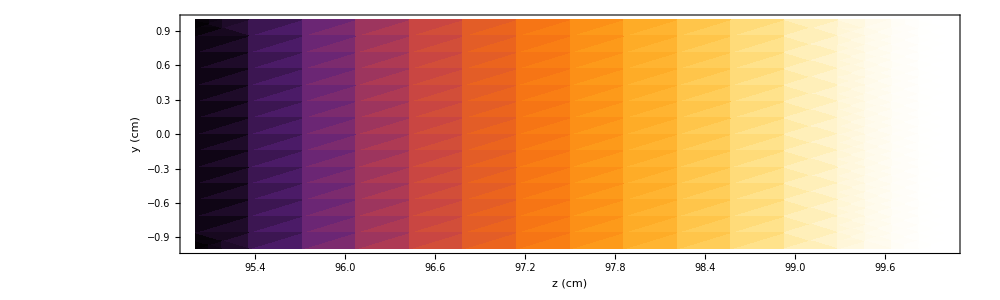

```mathematica
DensityPlot[sol[x0,y,z], {z,Lstick-5*Rrad,Lstick},{y,y0-Hstick/2,y0+Hstick/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->Full,ImageSize->{1000,400},FrameLabel->{"z (cm)", "y (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->0.3]
```

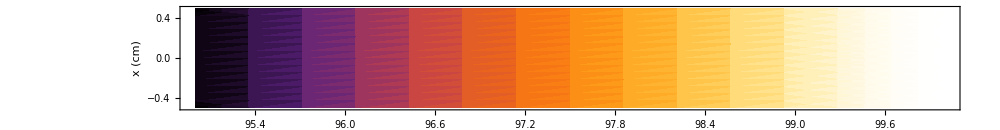

```mathematica
DensityPlot[sol[x,0,z], {z,Lstick-5*Rrad,Lstick},{x,x0-Wstick/2,x0+Wstick/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->Full,ImageSize->{1000,250},FrameLabel->{"z (cm)", "x (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->0.13]
```

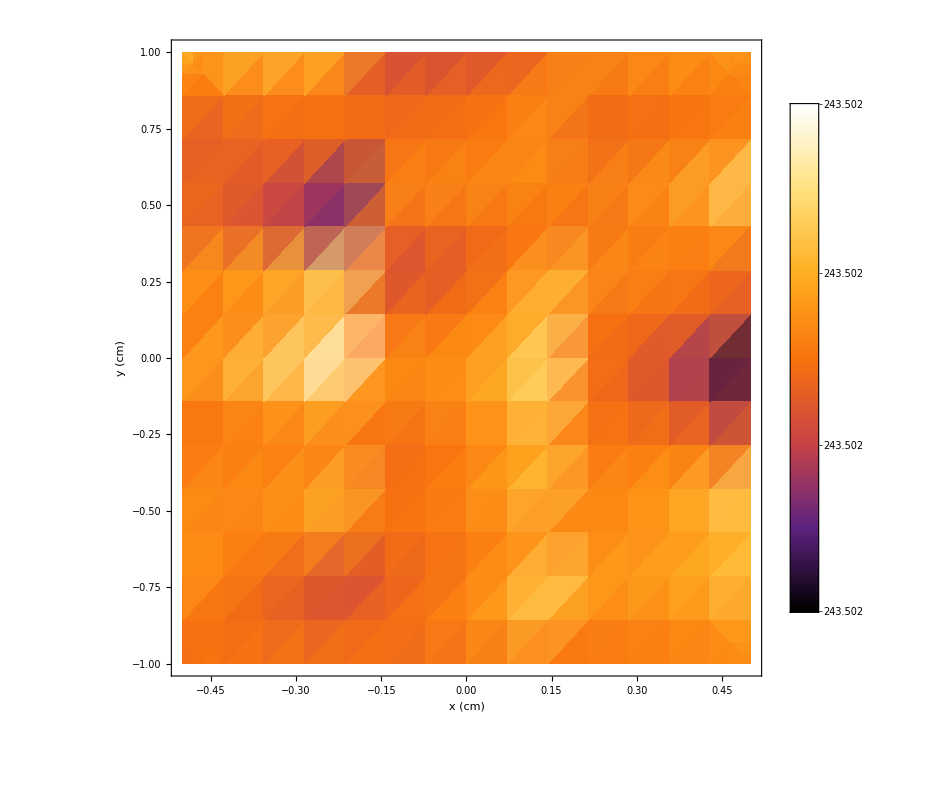

```mathematica
DensityPlot[sol[x,y,z0], {x,x0-Wstick/2,x0+Wstick/2},{y,y0-Hstick/2,x0+Hstick/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->Full,ImageSize->{800,800},FrameLabel->{"x (cm)", "y (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

```mathematica
SliceContourPlot3D[sol[x,y,z], "CenterPlanes",{x,x0-Wstick/2,x0+Wstick/2},{y,y0-Hstick/2,y0+Hstick/2},{z,0,Lstick}, PlotTheme->"Detailed",PlotRange->Full,  ImageSize->{800,800},PlotLabel->"T (^oC)",AxesLabel->{ "x (cm)", "y (cm)","z (cm)"},LabelStyle->{22,GrayLevel[0],Italic}]
```

-Graphics3D-

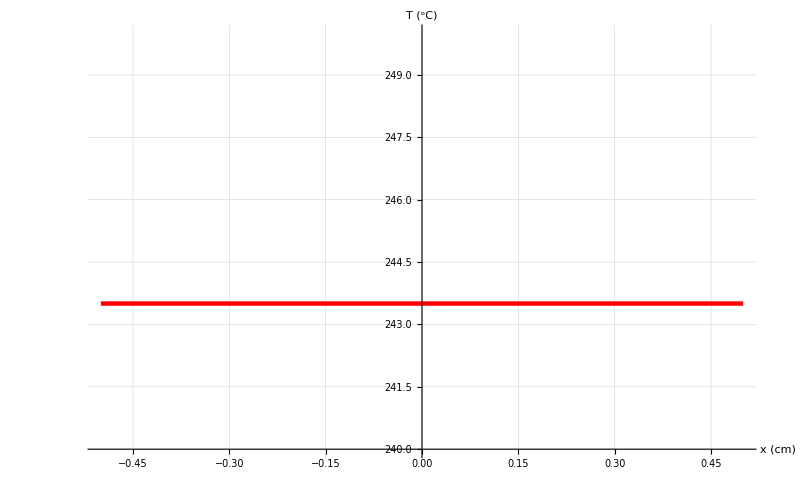

```mathematica
Plot[sol[x,y0,z0], {x,x0-Wstick/2,x0+Wstick/2},GridLines->Automatic,PlotRange->{240,250},AxesLabel->{"x (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

```mathematica
Plot[sol[x0,y,z0], {y,y0-Hstick/2,y0+Hstick/2},GridLines->Automatic,PlotRange->Full,AxesLabel->{"y (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

-Graphics-

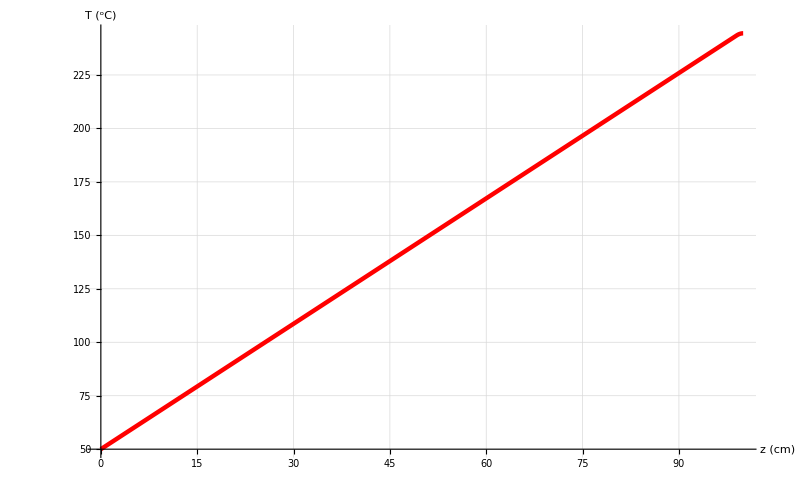

```mathematica
Plot[sol[x0,y0,z], {z,0,Lstick},GridLines->Automatic,PlotRange->Full,AxesLabel->{"z (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```